## Timings with varying Grid Sizes

```mathematica
sizes = 2^(Range[6] + 5);
```

```mathematica
globalMemTimes={0.006781,0.007112, 0.008976, 0.012738, 0.029692, 0.094213};
textureMemTimes={0.007021, 0.008074, 0.009907, 0.014670, 0.033109, 0.098999};
textureSharedMemTimes={0.007312, 0.007810, 0.009578, 0.013792, 0.035990, 0.097587};
textureNoCopyMemTimes={0.000699, 0.001098, 0.003788, 0.011974, 0.041241, 0.116662};
```

```mathematica
Grid[{sizes, globalMemTimes, textureMemTimes, textureSharedMemTimes, textureNoCopyMemTimes}, Frame->All]
```

64 | 128 | 256 | 512 | 1024 | 2048
0.006781 | 0.007112 | 0.008976 | 0.012738 | 0.029692 | 0.094213
0.007021 | 0.008074 | 0.009907 | 0.01467 | 0.033109 | 0.098999
0.007312 | 0.00781 | 0.009578 | 0.013792 | 0.03599 | 0.097587
0.000699 | 0.001098 | 0.003788 | 0.011974 | 0.041241 | 0.116662

```mathematica
globalMemPoints=MapThread[{#1,#2}&,{sizes,globalMemTimes}];
textureMemPoints=MapThread[{#1,#2}&,{sizes,textureMemTimes}];
textureSharedMemPoints=MapThread[{#1,#2}&,{sizes,textureSharedMemTimes}];
textureNoCopyMemPoints=MapThread[{#1,#2}&,{sizes,textureNoCopyMemTimes}];
```

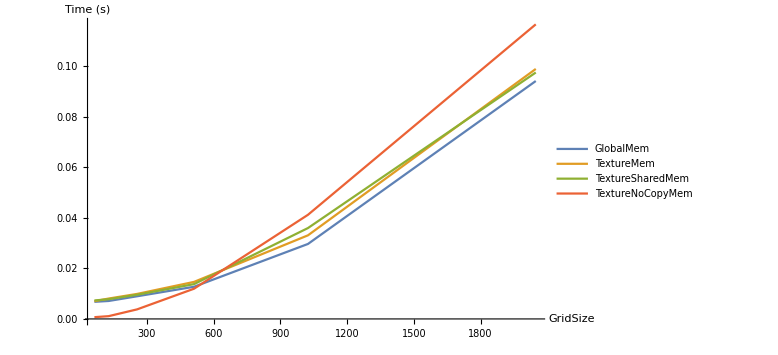

```mathematica
ListPlot[{globalMemPoints,textureMemPoints,textureSharedMemPoints,textureNoCopyMemPoints}, PlotRange->All,Joined->True, PlotLegends->{"GlobalMem", "TextureMem", "TextureSharedMem", "TextureNoCopyMem"},ImageSize->Large,AxesLabel->{"GridSize", "Time (s)"}]
```

## Analysis using Nvidia Profiler